# Alignment and Deformation

CSE 554 Module 5, Washington University in St. Louis (Fall 2015)

## Introduction

In this module, you will write algorithms that bring two meshes into alignment using translations, rotations, and local Laplacian-based deformations. Alignment is useful for establishing the correspondence between points on the two models, which is needed in many applications.

The required features include implementing rigid alignment (in both 2D and 3D) and basic Laplacian-based registration in 2D. Implementing rotation compensation for Laplacian-based registration and integrating it with Iterative Closest Point will earn you extra credits.

## Helpers

Sets the default folder to be the folder where this notebook is saved.

```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
```

### Vector operations and rotations

Vector normalization:

```mathematica
normalize[v_]:=v/√(v.v);
```

Rotate a 2D vector 90 degrees counter-clockwise:

```mathematica
perp[{x_,y_}]:={-y,x};
```

A 2D rotation matrix around the origin by angle α (should be multiplied to the LEFT of a point (represented as a column vector)):

```mathematica
Rot[a_]:=({{Cos[a], -Sin[a]}, {Sin[a], Cos[a]}});
```

3D rotation matrices around each coordinate axes by angle α:

```mathematica
RotX[a_]:=({{1, 0, 0}, {0, Cos[a], -Sin[a]}, {0, Sin[a], Cos[a]}});
RotY[a_]:=({{Cos[a], 0, Sin[a]}, {0, 1, 0}, {-Sin[a], 0, Cos[a]}});
RotZ[a_]:=({{Cos[a], -Sin[a], 0}, {Sin[a], Cos[a], 0}, {0, 0, 1}});
```

### Plotting points, correspondences, and axes

These functions display 2D and 3D points with a given color (e.g., Red, Blue, RGBColor[], GrayLevel[], etc.)

```mathematica
showPoints2D[pts_,col_]:=Graphics[{col,Map[Point,pts]},Frame->False,Axes->False];
```

```mathematica
showPoints3D[pts_,col_]:=Graphics3D[{col,Map[Point,pts]},Boxed->True,RotationAction->"Clip",Axes->False];
```

These functions display correspondence between two point sets as line segments between pairs of points.

```mathematica
showCorr2D[pts1_,pts2_]:=Graphics[{MapThread[Line[{#1,#2}]&,{pts1,pts2}]}];
```

```mathematica
showCorr3D[pts1_,pts2_]:=Graphics3D[{MapThread[Line[{#1,#2}]&,{pts1,pts2}]},Boxed->True,RotationAction->"Clip"];
```

These functions plot a given set of center and (un-oriented) axes in 2D and 3D.

```mathematica
showAxes2D[cent_,axes_]:=Graphics[{
RGBColor[1,0,0],Line[{cent-axes⟦1⟧,cent+axes⟦1⟧}],
RGBColor[0,1,0],Line[{cent-axes⟦2⟧,cent+axes⟦2⟧}],
GrayLevel[0],PointSize[0.04],Point[cent]}];
```

```mathematica
showAxes3D[cent_,axes_]:=Graphics3D[{Sphere[cent,0.05],
RGBColor[1,0,0],Cylinder[{cent-axes⟦1⟧,cent+axes⟦1⟧},0.02],
RGBColor[0,1,0],Cylinder[{cent-axes⟦2⟧,cent+axes⟦2⟧},0.02],
RGBColor[0,0,1],Cylinder[{cent-axes⟦3⟧,cent+axes⟦3⟧},0.02]}];
```

### Showing polylines

This function displays a 2D curve represented as a polyline {V,E}, where V is a list of vertex coordinates (with X,Y components), and E is a list of edges, each consisting of the indices of its two vertices. The function takes in an additional parameter of color (e.g., GrayLevel or RGB).

```mathematica
showCurve[{V_,E_},col_]:=Graphics[{{col,{Map[Line[V⟦#⟧]&,E]}},Map[Point,V]},Frame->False];
```

Same as above, except the vertices will not be displayed. This is helpful if you have lots of vertices in the curve.

```mathematica
showCurveNoPoints[{V_,E_},col_]:=Graphics[{col,Map[Line[V⟦#⟧]&,E]},Frame->False];
```

### Showing meshes

This function displays a 3D surface represented as a polygonal mesh {V,T}, where V is a list of vertex coordinates (with X,Y,Z components), and T is a list of polygons, each consisting of the indices of its vertices. The function takes in an additional parameter of color (e.g., GrayLevel or RGB).

```mathematica
showSurface[{V_,T_},col_]:=Graphics3D[{col,Map[Polygon[V⟦#⟧]&,T]},RotationAction->Clip,Lighting->"Neutral",Boxed->False];
```

Same as agove, except the polygon edges will not be displayed. This is helpful if you have lots of polygons in the surface.

```mathematica
showSurfaceNoEdges[{V_,T_},col_]:=Graphics3D[{col,EdgeForm[{}],Map[Polygon[V⟦#⟧]&,T]},RotationAction->Clip,Lighting->"Neutral",Boxed->False];
```

Same as agove, except ONLY the polygon edges will be displayed (i.e., a wire-frame). This is helpful when you want to show two surfaces at the same time (e.g., one showing only edges).

```mathematica
showSurfaceEdgesOnly[{V_,T_},col_]:=Graphics3D[{col,Map[Line[Append[V⟦#⟧,Last[V⟦#⟧]]]&,T]},RotationAction->Clip,Lighting->"Neutral",Boxed->False];
```

### Showing handles

This function displays the source and target locations of a set of handles:

```mathematica
showHandles[pts1_,pts2_]:=Module[{len=Length[pts1]},Graphics[{
Table[{If[closeby[pts1⟦i⟧,pts2⟦i⟧],Red,Blue],PointSize[0.015],Point[pts1⟦i⟧],PointSize[0.02],Point[pts2⟦i⟧]},{i,len}]}]];
closeby[p1_,p2_]:=((p1-p2).(p1-p2)<.00001);
```

## Algorithms

### Alignment with PCA [6 pts]

Algorithm 1: [2 pts] Create two functions that respectively compute the centroid location of a set of points pts (a list of 2D or 3D coordinates), and the PCA axes of the point set pts given its centroid cent. Your PCA axes should be a list of unit eigenvectors (with an arbitrary sign) ordered by decreasing order of their eigenvalues. Note that your code should work for both 2D and 3D point sets.

```mathematica
getCentroid[pts_]:=
```

```mathematica
getPCA[pts_,cent_]:=
```

Testing: [1 pt] Test your code on the following 2D and 3D examples. Each example has three point sets, one source set (ending in Src), and two target sets (ending in Tgt1 and Tgt2) that are transformed from the source. Visualize the points, computed centroids and axes using display functions showPoints and showAxes in the Helper. Compare with the pictures below (points in Src are red, Tgt1 are blue, Tgt2 are magenta, and the 1st, 2nd and 3rd axes are colored red, green, and blue).

Example 1 (2D):

```mathematica
(* number of points in both source and target*)
numPoints=100;
(* source: an ellipse with some noise *)
test2DSrc=Table[{2Cos[a],Sin[a]}+{RandomReal[.1],RandomReal[.1]},{a,0,2π,2π/numPoints}];
(* targets: rotated and translated sources *)
shift={1,2};angle=0.3;
test2DTgt1=Map[(#+shift)&,Transpose[Rot[angle].Transpose[test2DSrc]]];
shift={-1,2};angle=2;
test2DTgt2=Map[(#+shift)&,Transpose[Rot[angle].Transpose[test2DSrc]]];
```

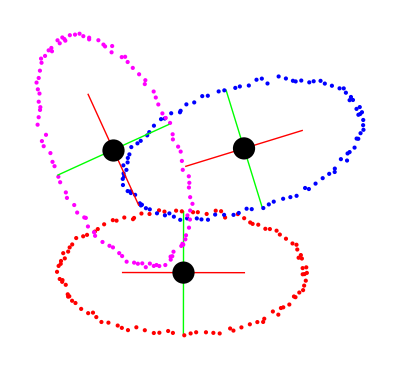

Example 2 (3D):

```mathematica
(* number of points in both source and target*)
numPoints=400;
(* source: an ellipsoid with some noise *)
sqrtnum=Sqrt[numPoints/2];
test3DSrc=Flatten[Table[
{2Cos[b]Cos[a],Cos[b]Sin[a],.5Sin[b]}+{RandomReal[.1],RandomReal[.1],RandomReal[.1]},{a,0,2π,π/sqrtnum},{b,-π/2+.2,π/2-.2,(π-.4)/sqrtnum}],1];
(* targets: rotated and translated sources *)
shift={1,1.5,1};angleX=0.3;angleY=0.7;
test3DTgt1=Map[(#+shift)&,Transpose[RotY[angleY].RotX[angleX].Transpose[test3DSrc]]];
shift={-1,2,-1};angleX=0.3;angleY=-2;
test3DTgt2=Map[(#+shift)&,Transpose[RotY[angleY].RotX[angleX].Transpose[test3DSrc]]];
```

Algorithm 2: [2 pts] Create two functions, one in 2D and one in 3D, that align two point sets (ptsSrc and ptsTgt) using their centroids and PCA axes, and output the transformed locations of ptsSrc. As mentioned in class, the PCA axes are un-oriented. To compute the rotation, your code needs to enumerate all possible ways of orienting the PCA axes (see slides). Pick the orientation choice that results in the least rotation angle. Note that the number of source and target points may be different.

```mathematica
alignPCA2D[ptsSrc_,ptsTgt_]:=
```

```mathematica
alignPCA3D[ptsSrc_,ptsTgt_]:=
```

Testing: [1 pt] In the 2D and 3D examples above, align the source (ending in Src) respectively to the two targets (ending in Tgt1 and Tgt2)  using PCA, and display the transformed sources along with the targets. The aligned source should exactly overlap with the first target (ending in Tgt1), but only roughly matching the shape of the second target (ending in Tgt2) (why?)

### Alignment with SVD [4 pts]

Algorithm 3: [3 pts] Create a function that aligns two corresponding point sets (ptsSrc and ptsTgt) using their centroids and the optimal rotation computed by SVD, and outputs the transformed locations of ptsSrc. You should assume that the two point sets have equal length, and the corresponding point of ptsSrc⟦i⟧ is ptsTgt⟦i⟧. Note that your code should work for both 2D and 3D point sets.

```mathematica
alignSVD[ptsSrc_,ptsTgt_]:=
```

Testing: [1 pt] Test your SVD alignment in a similar way as you did with PCA alignment, using the 2D and 3D examples above. In each example, the source should exactly overlap with both the first target (ending in Tgt1) and the second target (ending in Tgt2) after alignment (why?).

### Alignment with ICP [6 pts]

Algorithm 4: [1 pts] Create a function that takes in two point sets (ptsSrc and ptsTgt), which may have non-equal lengths, and output a list of points pts with the same length as ptsSrc, such that pts⟦i⟧ is the point among all points in ptsTgt that is closest to ptsSrc⟦i⟧. Your code should work for both 2D and 3D point sets.

```mathematica
getClosestPoints[ptsSrc_,ptsTgt_]:=
```

Testing: [1 pt] Test your code on the 2D and 3D examples below (each example consists of two sets of randomly generated points). Use the display function provided to check your result visually (due to randomness, your picture will be different). The red points are the first set and blue points are the second set, and a line is drawn between each source point and the closest target point computed by your function.

Example 1 (2D):

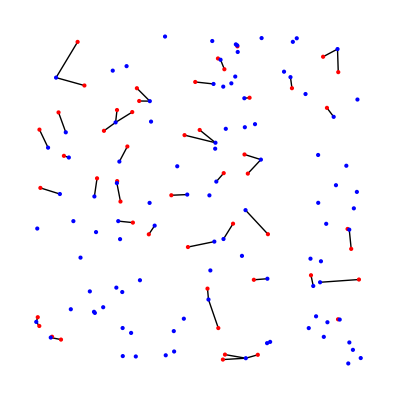

```mathematica
pts1=Table[RandomReal[1],{i,50},{2}];
pts2=Table[RandomReal[1],{i,100},{2}];
Show[{showCorr2D[pts1,getClosestPoints[pts1,pts2]],showPoints2D[pts1,Red],showPoints2D[pts2,Blue]}]
```

Example 2 (3D):

```mathematica
pts1=Table[RandomReal[1],{i,50},{3}];
pts2=Table[RandomReal[1],{i,100},{3}];
Show[{showCorr3D[pts1,getClosestPoints[pts1,pts2]],showPoints3D[pts1,Red],showPoints3D[pts2,Blue]}]
```

-Graphics3D-

Algorithm 5: [3 pts] Create a function that aligns two point sets (ptsSrc and ptsTgt) using iterative closest point (ICP), and outputs the transformed locations of ptsSrc. The stopping criteria of your iteration should be that the decrease in root mean squared distance (RMSD) after an iteration is smaller than a fixed small constant. Note that the two point sets may have non-equal lengths, and your code should work for both 2D and 3D point sets.

```mathematica
alignICP[ptsSrc_,ptsTgt_]:=
```

Testing: [1 pt] Align the source point sets test2DSrc and test3DSrc defined above respectively to the new targets defined below, test2DTgtNoise and test3DTgtNoise, which are generated by adding some outliers to the original targets, test2DTgt1 and test3DTgt1. The pictures below show the source (red) and target points in each case. Visually examine your alignment. In each case, the aligned source should exactly overlap with the ellipse (ellipsoid) part of the target.

```mathematica
test2DTgtNoise=Join[test2DTgt1,
Table[{RandomReal[{-2,-.5}],RandomReal[{2,3}]},{i,20}]];
```

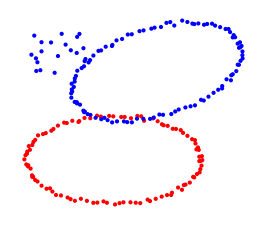

```mathematica
test3DTgtNoise=Join[test3DTgt1,
Table[{RandomReal[{-1.5,1.5}],RandomReal[{2,3}],RandomReal[{2,3}]},{i,50}]];
```

### Basic Laplacian deformation [6 pts]

Algorithm 6: [4 pts] Create a function that deforms an input curve by point handles. Use the basic form of the distortion energy term without compensating for rotation or scaling (Slide 11). The input/output are:
INPUT:
	 curve:  a polyline to be deformed (it could be either an open or closed curve).
	 vinds:  indices of vertices that are "handles"
	 tgts:  target locations of the handle vertices (i.e., the vertex in  curve with index  vinds⟦i⟧ should move to location  tgts⟦i⟧)
	 w: the balancing weight for the distortion energy (see Slide 47 of the lecture).	 
	
OUTPUT: a polyline with the deformed vertex locations.

```mathematica
deformLaplace[curve_,vinds_,tgts_,w_]:=
```

Testing 1: [1 pt] First, let's see if you get the matrix A and vector b correctly (recall that your deformed vertices are the solution of the equation A^T A x=A^T b). In the two simple examples below, closely follow the instructions and compare your results with mine. This basic exercise will be very helpful for debugging your code.

The input curve is a closed square, which has two corners (big red dots) as stationary handles:

```mathematica
squareCurve={{{0.,1.},{-1.,0.},{0.,-1.},{1.,0.}},{{1,2},{2,3},{3,4},{4,1}}};
squareVinds={1,3};
squareTgts={squareCurve⟦1,1⟧,squareCurve⟦1,3⟧};
Show[{showCurve[squareCurve,Red],showHandles[squareCurve⟦1,squareVinds⟧,squareTgts]}]
```

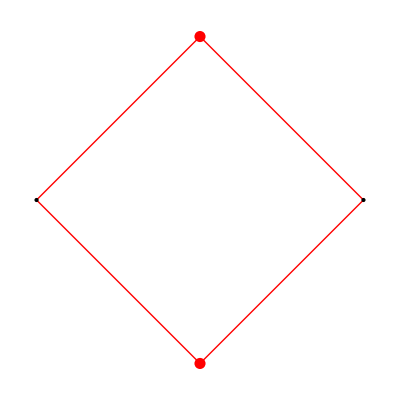

Run your own code on this example with weight w=1:

```mathematica
squareCurve2=deformLaplace[squareCurve,squareVinds,squareTgts,1];
```

Print out the A,b after you add the fitting terms and distortion terms. They should look like this (some rows of A, b may be swapped in your solution, which is ok):

After adding fitting terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),   b=(0.
1.
0.
-1.)

After adding Laplacian terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1/2 | 0 | -1/2
-1/2 | 1 | -1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 1 | -1/2 | 0
0 | -1/2 | 1 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 1 | -1/2
-1/2 | 0 | -1/2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | -1/2 | 1),   b=(0.
1.
0.
-1.
0.
1.
-1.
0.
0.
-1.
1.
0.)

The deformed curve should be identical to the original:

```mathematica
Show[{showCurve[squareCurve,Red],showCurve[squareCurve2,Blue],showHandles[squareCurve⟦1,squareVinds⟧,squareTgts]}]
```

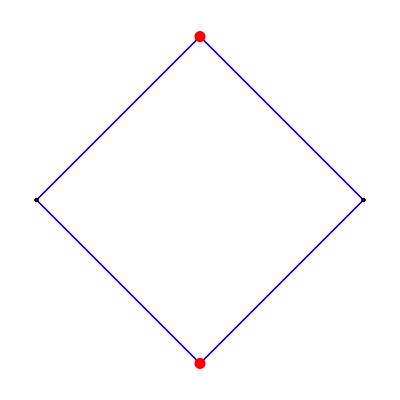

Now, let us move the bottom handle to a different location:

```mathematica
squareTgts2={squareCurve⟦1,1⟧,squareCurve⟦1,3⟧+{1,0}};
Show[{showCurve[squareCurve,Red],showHandles[squareCurve⟦1,squareVinds⟧,squareTgts2]}]
```

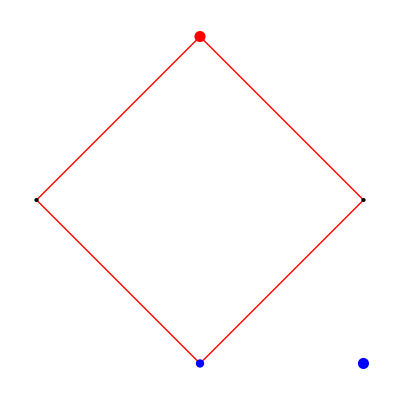

Run your code on this example with weight w=1:

```mathematica
squareCurve3=deformLaplace[squareCurve,squareVinds,squareTgts2,1];
Show[{showCurve[squareCurve,Red],showCurve[squareCurve3,Blue],showHandles[squareCurve⟦1,squareVinds⟧,squareTgts2]}]
```

Your A,b and deformed curve should look like:

After adding fitting terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),   b=(0.
1.
1.
-1.)

After adding Laplacian terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
1 | -1/2 | 0 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1/2 | 0 | -1/2
-1/2 | 1 | -1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 1 | -1/2 | 0
0 | -1/2 | 1 | -1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 1 | -1/2
-1/2 | 0 | -1/2 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | -1/2 | 1),   b=(0.
1.
1.
-1.
0.
1.
-1.
0.
0.
-1.
1.
0.)

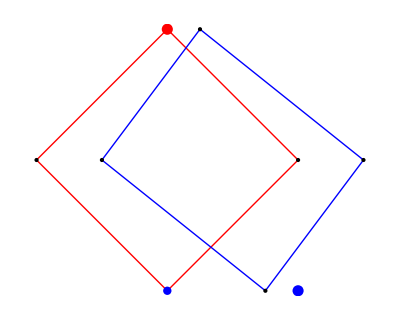

Note that the deformed curve does not exactly interpolate the target handle locations. Let's try with a smaller weight (w=0.1) so that we allow more distortion to the shape:

```mathematica
squareCurve3=deformLaplace[squareCurve,squareVinds,squareTgts2,.1];
Show[{showCurve[squareCurve,Red],showCurve[squareCurve3,Blue],showHandles[squareCurve⟦1,squareVinds⟧,squareTgts2]}]
```

Compare your A, b and deformed curve with these below:

After adding fitting terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),   b=(0.
1.
1.
-1.)

After adding Laplacian terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0.1 | -0.05 | 0 | -0.05 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.1 | -0.05 | 0 | -0.05
-0.05 | 0.1 | -0.05 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.05 | 0.1 | -0.05 | 0
0 | -0.05 | 0.1 | -0.05 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.05 | 0.1 | -0.05
-0.05 | 0 | -0.05 | 0.1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.05 | 0 | -0.05 | 0.1),   b=(0.
1.
1.
-1.
0.
0.1
-0.1
0.
0.
-0.1
0.1
0.)

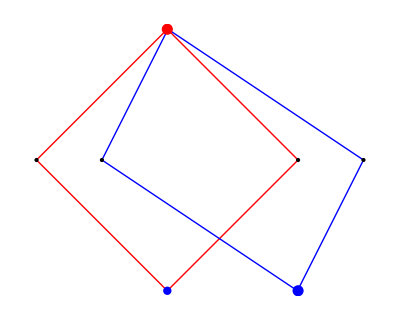

Your code should be capable of taking both open and closed curves. In this second example, the input curve is an open wave, whose two ends (big red dots) are stationary handles:

```mathematica
mCurve={{{0.,0.},{1.,1.},{2.,0.},{3.,1.},{4.,0.}},{{1,2},{2,3},{3,4},{4,5}}};
mVinds={1,5};
mTgts={mCurve⟦1,1⟧,mCurve⟦1,5⟧};
Show[{showCurve[mCurve,Red],showHandles[mCurve⟦1,mVinds⟧,mTgts]}]
```

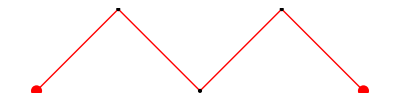

Run your code on this example with weight w=1:

```mathematica
mCurve2=deformLaplace[mCurve,mVinds,mTgts,1];
```

Your A, b should look like this:

After adding fitting terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),   b=(0.
0.
4.
0.)

After adding Laplacian terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0
-1/2 | 1 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 1 | -1/2 | 0 | 0
0 | -1/2 | 1 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1 | -1/2 | 0
0 | 0 | -1/2 | 1 | -1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1 | -1/2
0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1),   b=(0.
0.
4.
0.
-1.
-1.
0.
1.
0.
-1.
0.
1.
1.
-1.)

The deformed curve should be identical to the original:

```mathematica
Show[{showCurve[mCurve,Red],showCurve[mCurve2,Blue],showHandles[mCurve⟦1,mVinds⟧,mTgts]}]
```

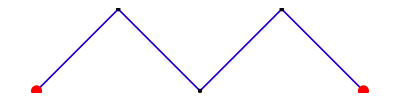

Testing 2: [1 pt] Now that you have a working piece of code, let's try on some larger examples.

First, consider this star curve with two stationary handles (red) and one moving handle (blue):

```mathematica
numPoints=100;numBumps=15;
starCurve={N[Table[{Cos[2π/numPoints*i],Sin[2π/numPoints*i]}*(1+.1*Sin[2*numBumps*π/numPoints*i]),{i,numPoints}]],Table[{i,Mod[i,numPoints]+1},{i,numPoints}]};
starVinds={1,numPoints/4,3*numPoints/4};
starTgts={starCurve⟦1,1⟧+{.3,0.1},starCurve⟦1,starVinds⟦2⟧⟧,starCurve⟦1,starVinds⟦3⟧⟧};
Show[{showCurve[starCurve,Red],showHandles[starCurve⟦1,starVinds⟧,starTgts]}]
```

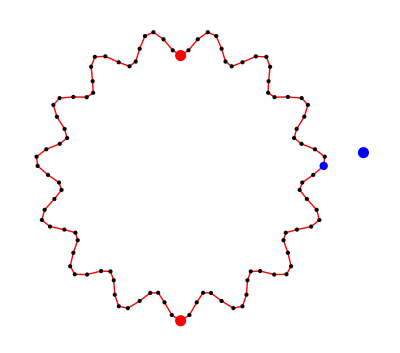

Run your code to deform it with weight w=1, and compare with my result:

```mathematica
starCurve2=deformLaplace[starCurve,starVinds,starTgts,1];
Show[{showCurve[starCurve,Red],showCurve[starCurve2,Blue],showHandles[starCurve⟦1,starVinds⟧,starTgts]}]
```

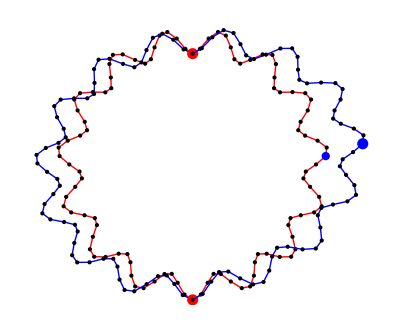

Now, try the following Manipulate applet that allows you to interactively change the moving handle location and the weight w:

```mathematica
Manipulate[
tgts={pt,starCurve⟦1,starVinds⟦2⟧⟧,starCurve⟦1,starVinds⟦3⟧⟧};
Show[{showCurveNoPoints[starCurve,Red],
showCurveNoPoints[deformLaplace[starCurve,starVinds,tgts,w],Blue],
showHandles[starCurve⟦1,starVinds⟧,starTgts]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],{{pt,starCurve⟦1,1⟧},{-1.5,-1.5},{1.5,1.5},Locator},
{{w,1},1,1000}]
```

Same exercise but now on an open spring with one stationary end (red) and one moving end (blue):

```mathematica
numPoints=100;numBumps=5;
springCurve={N[Table[{i/numPoints,5*Sin[2π*i*numBumps/numPoints]/numPoints},{i,numPoints}]],Table[{i,Mod[i,numPoints]+1},{i,numPoints-1}]};
springVinds={1,numPoints};
springTgts={First[springCurve⟦1⟧],Last[springCurve⟦1⟧]+{(√2)/2-1,-(√2)/2}};
Show[{showCurve[springCurve,Red],showHandles[springCurve⟦1,springVinds⟧,springTgts]}]
```

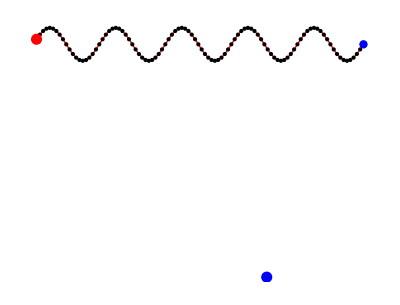

Run your code to deform it with weight w=1, and compare with my result:

```mathematica
springCurve2=deformLaplace[springCurve,springVinds,springTgts,1];
Show[{showCurve[springCurve,Red],showCurve[springCurve2,Blue],showHandles[springCurve⟦1,springVinds⟧,springTgts]}]
```

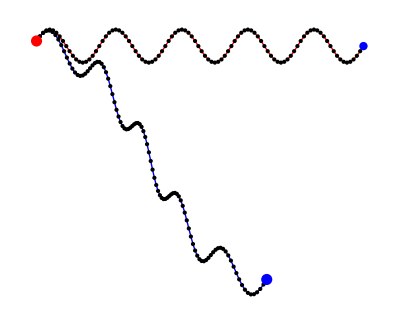

Now, run it in a Manipulate applet:

```mathematica
Manipulate[
tgts={First[springCurve⟦1⟧],pt};
Show[{showCurveNoPoints[springCurve,Red],
showCurveNoPoints[deformLaplace[springCurve,springVinds,tgts,w],Blue],
showHandles[springCurve⟦1,springVinds⟧,tgts]},PlotRange->{{-.2,1.2},{-.5,.5}}],{{pt,Last[springCurve⟦1⟧]},{-.2,-.5},{1.2,.5},Locator},
{{w,1},1,1000}]
```

### Laplacian deformation with transformation compensation [Extra credit +4 pts]

Algorithm 7: [+2 pts] Create a functions that deforms an input curve by point handles. Use the extended form of the distortion energy term that compensates for rotation or scaling (Slide 28). The input/output are the same as your basic Laplacian function above.

```mathematica
deformLaplaceRot[curve_,vinds_,tgts_,w_]:=
```

Testing 1: [+1 pt] Similarly as above, let's first make sure that you get the matrix A and vector b correctly.

Again, consider the input curve as a closed square, which has two corners (big red dots) as stationary handles:

```mathematica
squareCurve={{{0.,1.},{-1.,0.},{0.,-1.},{1.,0.}},{{1,2},{2,3},{3,4},{4,1}}};
squareVinds={1,3};
squareTgts={squareCurve⟦1,1⟧,squareCurve⟦1,3⟧};
Show[{showCurve[squareCurve,Red],showHandles[squareCurve⟦1,squareVinds⟧,squareTgts]}]
```

Run your own code on this example with weight w=1, and compare your A, b and deformed curve (which is identical to original) to below:

```mathematica
squareCurve2=deformLaplaceRot[squareCurve,squareVinds,squareTgts,1];
```

After adding fitting terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),   b=(0.
1.
0.
-1.)

After adding Laplacian terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
-0.75 | 0.375 | 0 | 0.375 | 0. | 0.375 | 0 | -0.375
0. | -0.375 | 0 | 0.375 | -0.75 | 0.375 | 0 | 0.375
0.375 | -0.75 | 0.375 | 0 | -0.375 | 0. | 0.375 | 0
0.375 | 0. | -0.375 | 0 | 0.375 | -0.75 | 0.375 | 0
0 | 0.375 | -0.75 | 0.375 | 0 | -0.375 | 0. | 0.375
0 | 0.375 | 0. | -0.375 | 0 | 0.375 | -0.75 | 0.375
0.375 | 0 | 0.375 | -0.75 | 0.375 | 0 | -0.375 | 0.
-0.375 | 0 | 0.375 | 0. | 0.375 | 0 | 0.375 | -0.75),   b=(0.
1.
0.
-1.
0
0
0
0
0
0
0
0)

```mathematica
Show[{showCurve[squareCurve,Red],showCurve[squareCurve2,Blue],showHandles[squareCurve⟦1,squareVinds⟧,squareTgts]}]
```

Now, let us move the bottom handle to a different location:

```mathematica
squareTgts2={squareCurve⟦1,1⟧,squareCurve⟦1,3⟧+{1,0}};
Show[{showCurve[squareCurve,Red],showHandles[squareCurve⟦1,squareVinds⟧,squareTgts2]}]
```

Run your code on this example with weight w=1, you should get the following results:

```mathematica
squareCurve3=deformLaplaceRot[squareCurve,squareVinds,squareTgts2,1];
Show[{showCurve[squareCurve,Red],showCurve[squareCurve3,Blue],showHandles[squareCurve⟦1,squareVinds⟧,squareTgts2]}]
```

After adding fitting terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0),   b=(0.
1.
1.
-1.)

After adding Laplacian terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
-0.75 | 0.375 | 0 | 0.375 | 0. | 0.375 | 0 | -0.375
0. | -0.375 | 0 | 0.375 | -0.75 | 0.375 | 0 | 0.375
0.375 | -0.75 | 0.375 | 0 | -0.375 | 0. | 0.375 | 0
0.375 | 0. | -0.375 | 0 | 0.375 | -0.75 | 0.375 | 0
0 | 0.375 | -0.75 | 0.375 | 0 | -0.375 | 0. | 0.375
0 | 0.375 | 0. | -0.375 | 0 | 0.375 | -0.75 | 0.375
0.375 | 0 | 0.375 | -0.75 | 0.375 | 0 | -0.375 | 0.
-0.375 | 0 | 0.375 | 0. | 0.375 | 0 | 0.375 | -0.75),   b=(0.
1.
1.
-1.
0
0
0
0
0
0
0
0)

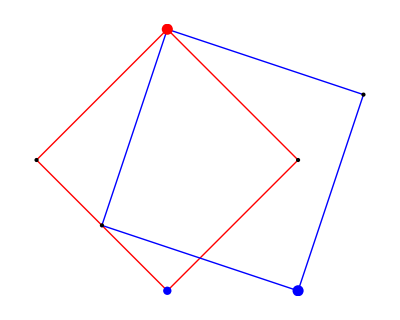

Note that the deformed curve now exactly interpolates the target handle locations without any shape distortion - thanks to rotation/scaling compenstation.

Now let's try on an open curve:

```mathematica
mCurve={{{0.,0.},{1.,1.},{2.,0.},{3.,1.},{4.,0.}},{{1,2},{2,3},{3,4},{4,5}}};
mVinds={1,5};
mTgts={mCurve⟦1,1⟧,mCurve⟦1,5⟧};
Show[{showCurve[mCurve,Red],showHandles[mCurve⟦1,mVinds⟧,mTgts]}]
```

Run your code on this example with weight w=1, and compare your results to below:

```mathematica
mCurve2=deformLaplaceRot[mCurve,mVinds,mTgts,1];
```

After adding fitting terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1),   b=(0.
0.
4.
0.)

After adding Laplacian terms:

A=(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0. | 0. | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0
0. | 0. | 0 | 0 | 0 | 0. | 0. | 0 | 0 | 0
0.375 | -0.75 | 0.375 | 0 | 0 | 0.375 | -5.55112×10^-17 | -0.375 | 0 | 0
-0.375 | -5.55112×10^-17 | 0.375 | 0 | 0 | 0.375 | -0.75 | 0.375 | 0 | 0
0 | 0.375 | -0.75 | 0.375 | 0 | 0 | -0.375 | 0. | 0.375 | 0
0 | 0.375 | 0. | -0.375 | 0 | 0 | 0.375 | -0.75 | 0.375 | 0
0 | 0 | 0.375 | -0.75 | 0.375 | 0 | 0 | 0.375 | 0. | -0.375
0 | 0 | -0.375 | 0. | 0.375 | 0 | 0 | 0.375 | -0.75 | 0.375
0 | 0 | 0 | -6.21725×10^-15 | 5.77316×10^-15 | 0 | 0 | 0 | -8.88178×10^-16 | 0.
0 | 0 | 0 | 0. | 8.88178×10^-16 | 0 | 0 | 0 | -6.66134×10^-15 | 4.88498×10^-15),   b=(0.
0.
4.
0.
0
0
0
0
0
0
0
0
0
0)

```mathematica
Show[{showCurve[mCurve,Red],showCurve[mCurve2,Blue],showHandles[mCurve⟦1,mVinds⟧,mTgts]}]
```

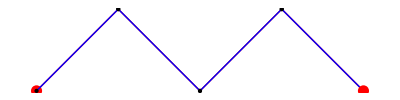

Testing 2: [+1 pt] Try on the same examples (star and spring) as in the previous section.

```mathematica
Manipulate[
tgts={pt,starCurve⟦1,starVinds⟦2⟧⟧,starCurve⟦1,starVinds⟦3⟧⟧};
Show[{showCurveNoPoints[starCurve,Red],
showCurveNoPoints[deformLaplace[starCurve,starVinds,tgts,w],Blue],
showHandles[starCurve⟦1,starVinds⟧,starTgts]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],{{pt,starCurve⟦1,1⟧},{-1.5,-1.5},{1.5,1.5},Locator},
{{w,1},1,1000}]
```

```mathematica
Manipulate[
tgts={First[springCurve⟦1⟧],pt};
Show[{showCurveNoPoints[springCurve,Red],
showCurveNoPoints[deformLaplaceRot[springCurve,springVinds,tgts,w],Blue],
showHandles[springCurve⟦1,springVinds⟧,tgts]},PlotRange->{{-.2,1.2},{-.5,.5}}],{{pt,Last[springCurve⟦1⟧]},{-.2,-.5},{1.2,.5},Locator},
{{w,1},1,1000}]
```

### ICP-Laplacian registration [Extra credit +3 pts]

Algorithm 8: [+2 pts] Create a function that deforms a source curve to the target using iterative closest points (ICP). The stopping criteria of your iteration should be that the decrease in root mean squared distance (RMSD) after an iteration is smaller than a fixed small constant. Input/outputs are:
INPUT:
	 curveSrc: source curve as a polyline
	 curveTgt: target curve as a polyline
	 w: weight for the distortion term
	 ϵ: threshold of RMSD change for termination
	 
OUTPUT: the deformed curve as a polyline

```mathematica
alignLaplace[curveSrc_,curveTgt_,w_,ϵ_]:=
```

Testing: [+1 pt] Use the  starCurve and  starCurve2 examples above to test your alignment, by aligning the former to the latter. Compare your result to that below (red: source starCurve; blue: target starCurve2; green: deformed source curve).

```mathematica
nstarCurve=alignLaplace[starCurve,starCurve2,100,.001];
Show[{showCurveNoPoints[starCurve,Red],showCurveNoPoints[starCurve2,Blue],showCurveNoPoints[nstarCurve,Green]}]
```

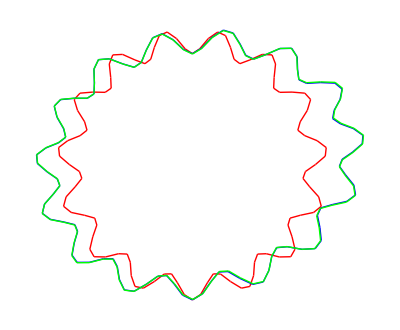

## Problems

Problem 1: [2 + Extra credit 2 pts] 2D brain alignment: the "brain_atlas.txt" file in the data folder contains a smoothed and simplified outline curve of a cross-section of a "standard" mouse brain (which we call "atlas"). There are 4 "brain_test?.txt" files, containing the brain outlines of different mouse subjects.  Try both PCA and ICP to align the atlas with the brain outlines in each file. You can load in the files using Get command; they are already in the polyline format. The pictures below show the atlas (red), the outline curve in "brain_test4.txt" (blue), and the results after PCA and ICP alignment.

Extra credit [+2 pts]: After rigid alignment, deform the atlas to the outline curve using Laplacian/ICP. Pick the parameters (weight w and stopping criteria ϵ) so that you get a good fit to the brain outline without significant distortion of the atlas' shape. An example is shown in the last picture below.

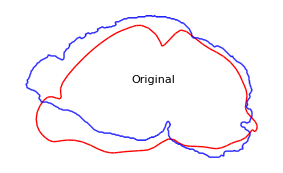
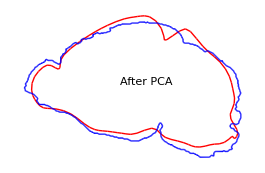
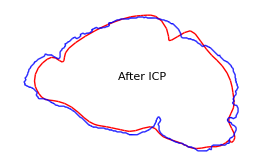
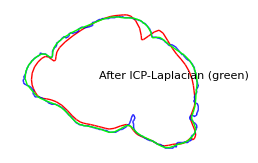

Problem 2: [2 pts] 3D bone alignment: the "bone_atlas.txt" file in the data folder contains a smoothed and simplified surface of a "standard" metatarsal bone (which we call "atlas"). There are several "bone_test?.txt" files, containing bone surfaces of different human subjects.  Try both PCA and ICP to align the atlas with each individual bone surface. You can load in the files using Get command; they are already in the mesh format.

The pictures below show the atlas (red), the bone surface in "bone_test2.txt" (blue), and the results after PCA and ICP alignment.

```mathematica
-Graphics3D-
-Graphics3D--Graphics3D-
```